This Notebook is made only for cases near tunnelling-without-barrier scenarios, that is, ω+2ω fields with π/2 phase shift and equal intensities.

## Configurations and Equations

### Field Configuration

#### Unit conversions

```mathematica
λToω[λ_]:=2π (0.052918 ×137)/λ
```

```mathematica
ωToλ[ω_]:=2π (0.052918 ×137)/ω
```

#### fieldConfig struct

```mathematica
fieldConfig::usage = "fieldConfig[] is a protected variable, which will act to hold an association of all its defining components, e.g., the time-dependence, wavelength, intensity";
Protect[fieldConfig];
(*this is the container (struct) where I can put all the field information into*)
```

```mathematica
E1
```

E1

```mathematica
fcSymbolic=fieldConfig["E1"->E1,"E2"->E2,"E0"->E0, "ϕ1"->ϕ1,"ϕ2"->ϕ2,"r"->1,"s"->2,"ω"->ω,"p"->4,"E3"->E3];
fcSymbolicToStrings={E1->"E1",E2->"E2",E0->"E0",ϕ1->"ϕ1",ϕ2->"ϕ2",ω->"ω",E3->"E3"};
```

#### TWOBfcSymbolic (the tunnelling without barrier scenario)

```mathematica
TWOBfcSymbolic=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2, "p"->4,
"ω"->ω]
```

makeFieldConfig[θ→π/4,E0→E0,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→ω]

#### makeFieldConfig

```mathematica
makeFieldConfig["E1"->E1_,"E2"->E2_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"E3"->E3_,"p"->p_,"phase"->phase_]:=fieldConfig[
"E1"->E1,
"E2"->E2,
"E0"->E0,
"E3"->E3,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω,"phase"->phase]
(* this shall generate a fieldConfig that can then be used for further computation of the field, the potential, the action etc. *)
```

I can overload this with a lot of definitions, e.g. income intensity etc.

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"p"->p_,"phase"->phase_]:=fieldConfig[
"E1"->Cos[θ]E0,
"E2"->Sin[θ]E0,
"E3"->0.01E0,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω,"phase"->phase]
```

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"p"->p_,"E3percent"->E3percent_,"phase"->phase_]:=fieldConfig[
"E1"->Cos[θ]E0,
"E2"->Sin[θ]E0,
"E3"->E3percent E0,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω,"phase"->phase]
```

A tunnelling-without-barrier scenario will (at least for now) always be this:

```mathematica
makeTWOBFieldConfig["E0"->E0_,"ω"->ω_,"E3percent"->E3percent_]:=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,"p"->4,
"ω"->ω]
```

```mathematica
makeAdjustableFieldConfig[phase_,mix_]:=makeFieldConfig["θ"->mix,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->4,"E3percent"->0.03,"phase"->phase]
```

```mathematica
field2fromConfig[makeAdjustableFieldConfig[0.1]][ωt]
makeAdjustableFieldConfig[ωt]
```

0.00320713 Cos[0.628319+4 ωt]

fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00320713,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395,phase→ωt]

#### test configuration

```mathematica
(*testfieldconfig=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->0]*)
test2fieldconfig=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->4,"E3"->0.01]
```

makeFieldConfig[θ→π/4,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395,p→4,E3→0.01]

```mathematica
testfieldconfigNo3=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->4,"E3percent"->0.03]
```

makeFieldConfig[θ→π/4,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395,p→4,E3percent→0.03]

```mathematica
field2fromConfig[test2fieldconfig][ωt]
```

0.01 Cos[4 ωt]

```mathematica
0.0010690449676496977 Cos[4 ωt]
```

0.00106904 Cos[4 ωt]

```mathematica
fieldFromConfig[test2fieldconfig][ωt]
```

0.00808122 Cos[ωt]-0.00808122 Cos[2 ωt]

```mathematica
fieldFromConfig[testfieldconfigNo3][ωt]
```

0.0755929 Cos[ωt]-0.0755929 Cos[2 ωt]

```mathematica
field2fromConfig[testfieldconfigNo3][ωt]
```

0.00320713 Cos[2 phase π+4 ωt]

### Target Configuration

```mathematica
targetConfig::usage = "targetConfig is a protected variable, which will hold the value for the ionization potential (as this is the only defining quantity for now)";
Protect[targetConfig];
```

#### κFromConfig

```mathematica
κFromConfig[targetConfig_]:= √(2 "Ip")/.(Association@@targetConfig)
```

#### Test target

```mathematica
testtargetconfig=targetConfig["Ip"->0.5] (*Hydrogen*)
```

targetConfig[Ip→0.5]

#### tcSymbolic

```mathematica
tcSymbolic=targetConfig["Ip"->Ip]
```

targetConfig[Ip→Ip]

### Field equation, vector potential and action

#### Field

```mathematica
fieldFromConfig[fieldConfig_][ωt_]:=Module[{f,fun},
f=Association@@fieldConfig;
"E1" Cos["r" ωt ]-"E2" Cos["s" ωt]/.f
]
field2fromConfig[fieldConfig_][ωt_] := Module[{f, fun},
f=Association@@fieldConfig;
"E3"Cos["p"ωt+2π×"phase"] /.f
]
```

```mathematica
Function[ωt,Module[{f,fun},f=Association@@fieldConfig;"E1" Sin["r" ωt+"ϕ1"]+"E2" Sin["s" ωt+"ϕ2"]/.f]]
```

Function[ωt,Module[{f,fun},f=Association@@fieldConfig;E1 Sin[r ωt+ϕ1]+E2 Sin[s ωt+ϕ2]/.f]]

```mathematica
fieldFromConfig[TWOBfcSymbolic][ωt]
field2fromConfig[TWOBfcSymbolic][ωt]
field2fromConfig[makeAdjustableFieldConfig[0.1]][ωt]
```

E1 Cos[ωt]-E2 Cos[2 ωt]

E3 Cos[2 phase π+4 ωt]

0.00320713 Cos[0.628319+4 ωt]

#### Potential

```mathematica
potential[ωt_]:=Module[{f,fun,field,pot,intfactor},
field=fieldFromConfig[fcSymbolic][ωt];
-1/ω×Integrate[field,ωt]//Simplify
]
potential2[ωt_]:=Module[{f,fun,field,pot,intfactor},
field=field2fromConfig[fcSymbolic][ωt];
-1/ω×Integrate[field,ωt]//Simplify
 ]
```

```mathematica
potentialFromConfig::usage="potentialFromConfig[fieldConfig] takes in a valid fieldConfig object and returns a vector potential A as a Function object, where A[t] is a numeric (or symbolic) vector potential";
potentialFromConfig[fieldConfig_][ωt_]:=Module[{f,fun,field,pot,intfactor},
f=Association@@fieldConfig;
potential[ωt]/.fcSymbolicToStrings/.f
]
potential2fromConfig[fieldConfig_][ωt_]:=Module[{f, fun, field,pot,intfactor},
f=Association@@fieldConfig;
potential2[ωt]/.fcSymbolicToStrings/.f
]
```

```mathematica
potentialFromConfig[TWOBfcSymbolic][ωt]
potential2fromConfig[TWOBfcSymbolic][ωt]
potential2fromConfig[makeAdjustableFieldConfig[0.1]][ωt]
Integrate[potential2fromConfig[makeAdjustableFieldConfig[0.1]][ωt],ωt]
```

(-2 E1 Sin[ωt]+E2 Sin[2 ωt])/(2 ω)

-(E3 Sin[2 phase π+4 ωt])/(4 ω)

-0.0140813 Sin[0.628319+4 ωt]

-0.0140813 ((-0.202254+0. ⅈ) Cos[4. ωt]+(0.146946+0. ⅈ) Sin[4. ωt])

#### Action

```mathematica
action[px_,py_,ωt_]=Module[{f,fun,field,field2, potx, poty,IntPotx,IntPoty,IntPotsqx,IntPotsqy},
field=fieldFromConfig[fcSymbolic][ωt];
potx=potentialFromConfig[fcSymbolic][ωt];
IntPotx=Integrate[potx,ωt];
IntPotsqx=Integrate[potx*potx,ωt];
field2=field2fromConfig[fcSymbolic][ωt];
poty = potential2fromConfig[fcSymbolic][ωt];
IntPoty=Integrate[poty,ωt];
IntPotsqy=Integrate[poty*poty,ωt];
(1/2 (px^2 ωt+py^2 ωt +2 (px IntPotx+py IntPoty)+IntPotsqx+IntPotsqy) +1/2 κ^2 ωt)
]
action2[px_,py_, ωt_]=Module[{f,fun,field,pot,IntPot,IntPotsq},
field=fieldFromConfig[fcSymbolic][ωt];
pot=potentialFromConfig[fcSymbolic][ωt];
IntPot=Integrate[pot,ωt];
IntPotsq=Integrate[pot*pot,ωt];
(1/2(px^2 ωt+py^2 ωt+2px IntPot+IntPotsq)+1/2 κ^2 ωt)
]
actionpert[py_,ωt_]=Module[{f,fun,field2,poty,IntPoty,IntPotsqy},
field2=field2fromConfig[fcSymbolic][ωt];
poty=potential2fromConfig[fcSymbolic][ωt];
IntPoty=Integrate[poty,ωt];
IntPotsqy=Integrate[poty*poty,ωt];
(1/2(2py IntPoty+IntPotsqy))
]
```

(κ^2 ωt)/2+1/2 (px^2 ωt+py^2 ωt+2 ((E3 py Cos[2 phase π+4 ωt])/(16 ω)+px ((E1 Cos[ωt] Sin[ϕ1])/ω+(E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E1 Cos[ϕ1] Sin[ωt])/ω+(E2 Cos[ϕ2] Sin[2 ωt])/(4 ω)))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt])/(4 ω^2)+(E3^2 (4 phase π+8 ωt-Sin[4 phase π+8 ωt]))/(256 ω^2))

(κ^2 ωt)/2+1/2 (px^2 ωt+py^2 ωt+2 px ((E1 Cos[ωt] Sin[ϕ1])/ω+(E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E1 Cos[ϕ1] Sin[ωt])/ω+(E2 Cos[ϕ2] Sin[2 ωt])/(4 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt])/(4 ω^2))

1/2 ((E3 py Cos[2 phase π+4 ωt])/(8 ω)+(E3^2 (4 phase π+8 ωt-Sin[4 phase π+8 ωt]))/(256 ω^2))

```mathematica
actionFromConfig[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
(*actionFromConfig[fieldConfig,targetConfig][px,py,ωt]=*)
Module[{f,fun,field,field2, potx, poty,IntPotx,IntPoty,IntPotsqx,IntPotsqy},
f=Association@@fieldConfig;

action[px,py,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]

]
basicActionFromConfig[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
(*actionFromConfig[fieldConfig,targetConfig][px,py,ωt]=*)
Module[{g,fun,field,pot,IntPot,IntPotsq},
g=Association@@fieldConfig;

action2[px,py,ωt]/.fcSymbolicToStrings/.g/.κ->κFromConfig[targetConfig]

]
perturbedActionFromConfig[fieldConfig_][py_,ωt_]:=
Module[{g,fun,field2,poty,IntPoty,IntPotsqy},
g=Association@@fieldConfig;
actionpert[py,ωt]/.fcSymbolicToStrings/.g]
```

```mathematica
actionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
basicActionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
perturbedActionFromConfig[TWOBfcSymbolic][py,ωt]
perturbedActionFromConfig[makeAdjustableFieldConfig[0.2]][0.1,ωt]
```

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 (px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(E3 py Cos[2 phase π+4 ωt])/(16 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2)+(E3^2 (4 phase π+8 ωt-Sin[4 phase π+8 ωt]))/(256 ω^2))

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

1/2 ((E3 py Cos[2 phase π+4 ωt])/(8 ω)+(E3^2 (4 phase π+8 ωt-Sin[4 phase π+8 ωt]))/(256 ω^2))

1/2 (0.000704066 Cos[1.25664+4 ωt]+0.0000123927 (2.51327+8 ωt-Sin[2.51327+8 ωt]))

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 (px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(E3 py Cos[4 ωt])/(16 ω))+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2)+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

1/2 ((E3 py Cos[4 ωt])/(8 ω)+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2))

```mathematica
actionFromConfig[testfieldconfigNo3,testtargetconfig][0.2,0.,0.5]
basicActionFromConfig[testfieldconfigNo3,testtargetconfig][0.2,0,0.5]
```

0.458683

0.457373

```mathematica
Block[{px=0.3, py=0.4, fc=test2fieldconfig, ωt=0.+0.4ⅈ, tc=testtargetconfig},
(*action[px,py,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]*)

dSdωt[fc,tc][px,py,ωt]
]
```

0.623961+0.00880283 ⅈ

### Derivatives of the action

#### First derivative

```mathematica
dS0dωt[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
Module[{drv,pp,pq},
drv[pp_,pq_,x_]=D[basicActionFromConfig[fieldConfig,targetConfig][pp,pq,x],x];

Function[{pp,pq,x},
drv[pp,pq,x]
][px,py,ωt]

]
dSdωt[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
Module[{drv,pp,pq},
drv[pp_,pq_,x_]=D[actionFromConfig[fieldConfig,targetConfig][pp,pq,x],x];

Function[{pp,pq,x},
drv[pp,pq,x]
][px,py,ωt]

]

dδSdωt[fieldConfig_][py_,ωt_] :=
Module[{drv,pq},
drv[pq_,x_] = D[perturbedActionFromConfig[fieldConfig][pq,x],x];

Function[{pq,x},
drv[pq,x]
][py,ωt]

]
```

```mathematica
dδSdωt[testfieldconfigNo3][0.1,ωt]
```

1/2 (0.0088126 (1/2-1/2 Cos[8 ωt])-0.0187751 Sin[4 ωt])

```mathematica
dSdωt[testfieldconfigNo3,testtargetconfig][0.2,0.3,0.3]
```

0.561649

#### Second derivative

```mathematica
d2Sdωt2[fieldConfig_,targetConfig_][px_,py_,ωt_]:=Module[{drv2,pp,pq}, (*he did this when drunk*)
drv2[pp_,pq_,x_]=D[actionFromConfig[fieldConfig,targetConfig][pp, pq, x],{x,2}];

Function[{pp,pq, x},
drv2[pp, pq, x]
][px, py, ωt]

]
```

```mathematica
d2Sdωt2[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
```

1/2 (2 (px (-(E1 Cos[ωt])/ω+(E2 Cos[2 ωt])/ω)-(E3 py Cos[4 ωt])/ω)+(E3^2 Sin[8 ωt])/(4 ω^2)+(2 E1 E2 Sin[ωt]-6 E1 E2 Sin[3 ωt]-4 E1^2 Sin[2 (π/2+ωt)]-2 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

```mathematica
d2Sdωt2[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
```

1/2 (2 px (-(E1 Cos[ωt])/ω+(E2 Cos[2 ωt])/ω)+(2 E1 E2 Sin[ωt]-6 E1 E2 Sin[3 ωt]-4 E1^2 Sin[2 (π/2+ωt)]-2 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

### Derived quantities about the setup

#### Keldysh parameter

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 UpondFromConfig[fieldConfig])]
```

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_,"Upfixed"]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 (("E0")/("ω"))^2/.(Association@@fieldConfig))]
```

```mathematica
KeldyshγFromConfig[testfieldconfig,testtargetconfig]
```

0.673718

#### ponderomotive energy (Upond)

```mathematica
UpondFromConfig[fieldConfig_]:=5/32(("E0")/("ω"))^2+(1/4("E3")/("ω"))^2/.(Association@@fieldConfig);
```

```mathematica
UpondFromConfig[makeAdjustableFieldConfig[0.01]]
```

0.55081

#### Strong-field parameter

```mathematica
zfFromConfig[fieldConfig_]:=("E0")^2/("ω")^3/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[fieldConfig_,"Updirect"]:=UpondFromConfig[fieldConfig]/("ω")/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[testfieldconfig]
```

61.9085

## Saddle points

### Utilities for the saddle point search

#### findωtBorder[]: Finding the border between the two bands

```mathematica
findωtBorder[fieldConfig_]:=
Module[{borderrange,bordertime,zeros},
borderrange={π/2,(3π)/4};
zeros=Select[ωt/.
Quiet@NSolve[
fieldFromConfig[fieldConfig][ωt]
==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&];
bordertime=Select[zeros, borderrange[[1]]<=Re[Round[#,10^-5]]<=borderrange[[2]]&][[1]];
Return[bordertime]
]
```

```mathematica
findωtBorder[testfieldconfigNo3]
dSdωt[testfieldconfigNo3,testtargetconfig][px,py,ωt]
```

2.0944

0.5+1/2 (px^2+py^2+77.1103 (0.0142857-0.0114286 Cos[ωt]+0.0114286 Cos[3 ωt]+0.0114286 Cos[2 (π/2+ωt)]+0.00285714 Cos[2 (-π/2+2 ωt)])+2 px (-1.3276 Sin[ωt]+0.6638 Sin[2 ωt]))

#### Grid of seeds

```mathematica
SeedsGrid[fieldConfig_]:=Module[{},
(*Print[fieldConfig];*)
Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π,7/5 π,0.5},
{ωtimag0,0,If[(Association@@fieldConfig)[["E1"]]!=0 && (*I added this bc I don't want to divide by zero. I think it's not the best way to do it though*)
((Association@@fieldConfig)[["E2"]])/((Association@@fieldConfig)[["E1"]])<0.1,6π,8/5 π],0.5}
],1]
](*
*)
```

Plot these in the real and imaginary plane. Don’t forget. Also remove the 4-omega for the findSaddles[] and use perturbation theory instead.

```mathematica
SeedsGrid[testfieldconfigNo3]
dSdωt[testfieldconfigNo3,testtargetconfig][px,py,ωt]
```

{-3.14159+0. ⅈ,-3.14159+0.5 ⅈ,-3.14159+1. ⅈ,-3.14159+1.5 ⅈ,-3.14159+2. ⅈ,-3.14159+2.5 ⅈ,-3.14159+3. ⅈ,-3.14159+3.5 ⅈ,-3.14159+4. ⅈ,-3.14159+4.5 ⅈ,-3.14159+5. ⅈ,-2.64159+0. ⅈ,-2.64159+0.5 ⅈ,-2.64159+1. ⅈ,-2.64159+1.5 ⅈ,-2.64159+2. ⅈ,-2.64159+2.5 ⅈ,-2.64159+3. ⅈ,-2.64159+3.5 ⅈ,-2.64159+4. ⅈ,-2.64159+4.5 ⅈ,-2.64159+5. ⅈ,-2.14159+0. ⅈ,-2.14159+0.5 ⅈ,-2.14159+1. ⅈ,-2.14159+1.5 ⅈ,-2.14159+2. ⅈ,-2.14159+2.5 ⅈ,-2.14159+3. ⅈ,-2.14159+3.5 ⅈ,-2.14159+4. ⅈ,-2.14159+4.5 ⅈ,-2.14159+5. ⅈ,-1.64159+0. ⅈ,-1.64159+0.5 ⅈ,-1.64159+1. ⅈ,-1.64159+1.5 ⅈ,-1.64159+2. ⅈ,-1.64159+2.5 ⅈ,-1.64159+3. ⅈ,-1.64159+3.5 ⅈ,-1.64159+4. ⅈ,-1.64159+4.5 ⅈ,-1.64159+5. ⅈ,-1.14159+0. ⅈ,-1.14159+0.5 ⅈ,-1.14159+1. ⅈ,-1.14159+1.5 ⅈ,-1.14159+2. ⅈ,-1.14159+2.5 ⅈ,-1.14159+3. ⅈ,-1.14159+3.5 ⅈ,-1.14159+4. ⅈ,-1.14159+4.5 ⅈ,-1.14159+5. ⅈ,-0.641593+0. ⅈ,-0.641593+0.5 ⅈ,-0.641593+1. ⅈ,-0.641593+1.5 ⅈ,-0.641593+2. ⅈ,-0.641593+2.5 ⅈ,-0.641593+3. ⅈ,-0.641593+3.5 ⅈ,-0.641593+4. ⅈ,-0.641593+4.5 ⅈ,-0.641593+5. ⅈ,-0.141593+0. ⅈ,-0.141593+0.5 ⅈ,-0.141593+1. ⅈ,-0.141593+1.5 ⅈ,-0.141593+2. ⅈ,-0.141593+2.5 ⅈ,-0.141593+3. ⅈ,-0.141593+3.5 ⅈ,-0.141593+4. ⅈ,-0.141593+4.5 ⅈ,-0.141593+5. ⅈ,0.358407+0. ⅈ,0.358407+0.5 ⅈ,0.358407+1. ⅈ,0.358407+1.5 ⅈ,0.358407+2. ⅈ,0.358407+2.5 ⅈ,0.358407+3. ⅈ,0.358407+3.5 ⅈ,0.358407+4. ⅈ,0.358407+4.5 ⅈ,0.358407+5. ⅈ,0.858407+0. ⅈ,0.858407+0.5 ⅈ,0.858407+1. ⅈ,0.858407+1.5 ⅈ,0.858407+2. ⅈ,0.858407+2.5 ⅈ,0.858407+3. ⅈ,0.858407+3.5 ⅈ,0.858407+4. ⅈ,0.858407+4.5 ⅈ,0.858407+5. ⅈ,1.35841+0. ⅈ,1.35841+0.5 ⅈ,1.35841+1. ⅈ,1.35841+1.5 ⅈ,1.35841+2. ⅈ,1.35841+2.5 ⅈ,1.35841+3. ⅈ,1.35841+3.5 ⅈ,1.35841+4. ⅈ,1.35841+4.5 ⅈ,1.35841+5. ⅈ,1.85841+0. ⅈ,1.85841+0.5 ⅈ,1.85841+1. ⅈ,1.85841+1.5 ⅈ,1.85841+2. ⅈ,1.85841+2.5 ⅈ,1.85841+3. ⅈ,1.85841+3.5 ⅈ,1.85841+4. ⅈ,1.85841+4.5 ⅈ,1.85841+5. ⅈ,2.35841+0. ⅈ,2.35841+0.5 ⅈ,2.35841+1. ⅈ,2.35841+1.5 ⅈ,2.35841+2. ⅈ,2.35841+2.5 ⅈ,2.35841+3. ⅈ,2.35841+3.5 ⅈ,2.35841+4. ⅈ,2.35841+4.5 ⅈ,2.35841+5. ⅈ,2.85841+0. ⅈ,2.85841+0.5 ⅈ,2.85841+1. ⅈ,2.85841+1.5 ⅈ,2.85841+2. ⅈ,2.85841+2.5 ⅈ,2.85841+3. ⅈ,2.85841+3.5 ⅈ,2.85841+4. ⅈ,2.85841+4.5 ⅈ,2.85841+5. ⅈ,3.35841+0. ⅈ,3.35841+0.5 ⅈ,3.35841+1. ⅈ,3.35841+1.5 ⅈ,3.35841+2. ⅈ,3.35841+2.5 ⅈ,3.35841+3. ⅈ,3.35841+3.5 ⅈ,3.35841+4. ⅈ,3.35841+4.5 ⅈ,3.35841+5. ⅈ,3.85841+0. ⅈ,3.85841+0.5 ⅈ,3.85841+1. ⅈ,3.85841+1.5 ⅈ,3.85841+2. ⅈ,3.85841+2.5 ⅈ,3.85841+3. ⅈ,3.85841+3.5 ⅈ,3.85841+4. ⅈ,3.85841+4.5 ⅈ,3.85841+5. ⅈ,4.35841+0. ⅈ,4.35841+0.5 ⅈ,4.35841+1. ⅈ,4.35841+1.5 ⅈ,4.35841+2. ⅈ,4.35841+2.5 ⅈ,4.35841+3. ⅈ,4.35841+3.5 ⅈ,4.35841+4. ⅈ,4.35841+4.5 ⅈ,4.35841+5. ⅈ}

0.5+1/2 (px^2+py^2+0.0088126 (1/2-1/2 Cos[8 ωt])+77.1103 (0.0142857-0.0114286 Cos[ωt]+0.0114286 Cos[3 ωt]+0.0114286 Cos[2 (π/2+ωt)]+0.00285714 Cos[2 (-π/2+2 ωt)])+2 (px (-1.3276 Sin[ωt]+0.6638 Sin[2 ωt])-0.0938755 py Sin[4 ωt]))

### Finding saddle points

#### findSaddles[]

```mathematica
findSaddles::usage="findSaddles[fieldConfig_,targetConfig_][px_] searches for solutions of the first derivative of the action within -π and 2π. It return a list of phase values, ordered by their real part, which can then be sorted by the classification functions";
findSaddles[fieldConfig_,targetConfig_][pp_,pq_]:= (*we can ignore the third field so that it doesn't create new saddle points while also seeing how it affects the intitial ones :) *)
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dS0dωt[fieldConfig,targetConfig][pp,pq,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dS0dωt[fieldConfig,targetConfig][pp,pq,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-2<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
findgloopySaddles[fieldConfig_,targetConfig_][pp_,pq_]:= (*we can ignore the third field so that it doesn't create new saddle points while also seeing how it affects the intitial ones :) *)
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dSdωt[fieldConfig,targetConfig][pp,pq,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dSdωt[fieldConfig,targetConfig][pp,pq,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-2<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
```

```mathematica
findSaddles[testfieldconfigNo3,testtargetconfig][0.0,0.0]
findgloopySaddles[testfieldconfigNo3,testtargetconfig][0.,0.38]
```

{-0.950079+0.70285 ⅈ,-7.59471×10^-17+1.04849 ⅈ,0.950079+0.70285 ⅈ,3.14159+0.357211 ⅈ,5.33311+0.70285 ⅈ}

{-1.20764+0.994025 ⅈ,-0.921274+0.644619 ⅈ,0.0845828+0.767823 ⅈ,0.753175+0.726752 ⅈ,1.31983+0.905668 ⅈ,2.43161+1.18855 ⅈ,3.16327+0.372501 ⅈ,3.80123+1.21056 ⅈ,5.36191+0.644619 ⅈ}

```mathematica
field2fromConfig[test2fieldconfig][ωt]
```

0.00106904 Cos[4 ωt]

```mathematica
Timing[findSaddles[test2fieldconfig,testtargetconfig][0.1,0.1]]
```

{0.,findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1]}

```mathematica
Last[%206]
```

findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1]

```mathematica
ResourceFunction["Intercepts"][%207,{findSaddles[fieldConfig["E1"->0.07559289460184544,"E2"->0.07559289460184544,"E3"->0.0010690449676496977,"E0"->0.10690449676496976,"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,"p"->4,"ω"->0.056939529014612654],targetConfig["Ip"->0.5]][0.1,0.1],y}]
```

[findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1],{findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1],y}]

#### Plotting fields and saddles

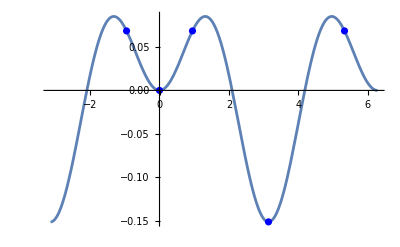

```mathematica
Block[{px=0., py=0., fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
Show[{
Plot[fieldFromConfig[fc][ωt],{ωt,-π,2π}],
ListPlot[{Re[#],fieldFromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
(*,ListPlot[{Re[#],fieldFromConfig[testfieldconfig1][Re[#]]}&/@findSaddles[testfieldconfig1,testtargetconfig][4],PlotStyle->Red]*)
}]
]
```

```mathematica
DynamicModule[{fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
Manipulate[
saddles=findSaddles[fc,tc][px,py];
Show[{
ListLinePlot3D[Table[{ωt,fieldFromConfig[fc][ωt],field2fromConfig[fc][ωt]},{ωt,-π+0.5,2π-0.5,.1}]],
ListPointPlot3D[{Re[#],fieldFromConfig[fc][Re[#]],field2fromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
}]
,{px,-3,+3} ,{py,-3,+3}]
]
```

Part::partw: Part 3 of {} does not exist.

```mathematica
DynamicModule[{fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
Manipulate[
saddles=findgloopySaddles[fc,tc][px,py];
Show[{
ListLinePlot3D[Table[{ωt,fieldFromConfig[fc][ωt],field2fromConfig[fc][ωt]},{ωt,-π+0.5,2π-0.5,.1}]],
ListPointPlot3D[{Re[#],fieldFromConfig[fc][Re[#]],field2fromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
}]
,{px,-3,+3} ,{py,-3,+3}]
]
findωtBorder[testfieldconfigNo3]
```

2.0944

FindRoot::nlnum: The function value {0.5+0.5 ((18.+0. ⅈ)+0.0000123927 (8.-8. Cos[«1»])+2. ((-9.75504×10^-16+0. ⅈ)-0.042244 Sin[«1»]))} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0. ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00320713,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][-3,-3,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((15.8335+1.24927×10^-15 ⅈ)+0.0000123927 (8.-8. Cosh[«1»])+2. ((-1.30264×10^-15-4.41571 ⅈ)+(0.+0.042244 ⅈ) Sinh[«1»]))} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0.5 ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00320713,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][-3,-3,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((2.25731+7.1896×10^-15 ⅈ)+0.0000123927 (8.-8. Cosh[«1»])+2. ((-2.58766×10^-15-11.9031 ⅈ)+(0.+0.042244 ⅈ) Sinh[«1»]))} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+1. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00320713,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][-3,-3,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value ωtSeed in search specification {ωtx,ωtSeed} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 3 of {} does not exist.

2.0944

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,-,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value ωtSeed in search specification {ωtx,ωtSeed} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.5+0.5 ((2.6244+0. ⅈ)+2. ((5.26772×10^-16+0. ⅈ)-(4.59857×10^-17+0. ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0. ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((0.341976+1.36708×10^-15 ⅈ)+2. ((7.03427×10^-16+2.38448 ⅈ)-(1.73007×10^-16+0.340473 ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0.5 ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((-19.6814+1.36239×10^-14 ⅈ)+2. ((1.39734×10^-15+6.42768 ⅈ)-(1.25579×10^-15+2.56185 ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+1. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value ωtSeed in search specification {ωtx,ωtSeed} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.5+0.5 ((2.6244+0. ⅈ)+2. ((5.26772×10^-16+0. ⅈ)-(4.59857×10^-17+0. ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0. ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((0.341976+1.36708×10^-15 ⅈ)+2. ((7.03427×10^-16+2.38448 ⅈ)-(1.73007×10^-16+0.340473 ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0.5 ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((-19.6814+1.36239×10^-14 ⅈ)+2. ((1.39734×10^-15+6.42768 ⅈ)-(1.25579×10^-15+2.56185 ⅈ) --)+(--)^2)} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+1. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][1.62,--,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value ωtSeed in search specification {ωtx,ωtSeed} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 3 of {} does not exist.

ListPointPlot3D::ldata: findgloopySaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][{0,fieldFromConfig[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395]][0],field2fromConfig[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395]][0]},{«1»}] is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in ….

FindRoot::nlnum: The function value {0.5+0.5 ((0.539412+0. ⅈ)+0.000550788 (8.-8. Cos[«1»])-0.137893 Sin[(12.5664+0. ⅈ)+Times[«2»]])} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0. ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0,-0.734447,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((-1.62709+1.24927×10^-15 ⅈ)+0.000550788 (8.-8. Cosh[«1»])+(0.+0.137893 ⅈ) Sinh[(2.+12.5664 ⅈ)+Times[«2»]])} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+0.5 ⅈ}.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0,-0.734447,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.5+0.5 ((-15.2033+7.1896×10^-15 ⅈ)+0.000550788 (8.-8. Cosh[«1»])+(0.+0.137893 ⅈ) Sinh[(4.+12.5664 ⅈ)+Times[«2»]])} is not a list of numbers with dimensions {1} at {ωtx} = {-3.14159+1. ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dSdωt[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0,-0.734447,ωtx]==0,{ωtx,ωtSeed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value ωtSeed in search specification {ωtx,ωtSeed} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 3 of {} does not exist.

### Classifying saddle points

#### ClassifySaddles[]

```mathematica
classifygloops[fieldConfig_,targetConfig_][saddlesList_,gloopList_]:=Module[{
saddles,gloops,
ABCsaddles,Agloop,Bgloop,Cgloop,
ABCsaddlesclassified,Dsaddle,Dgloop,
classifiedsaddles,classifiedgloops,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
gloops=SortBy[gloopList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

nsaddles1cycle=Length[
Select[saddles,Re[saddles[[1]]]<=Re[#]<=Re[saddles[[1]]]+2π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
Agloop=Nearest[gloops,ACsaddles[[1]]];
Bgloop=Nearest[gloops,ABCsaddles[[3]]];
Cgloop=Nearest[gloops,ACsaddles[[2]]];
(*Print["ACSaddles: ",ACsaddles];*)

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} };
Agloop=Nearest[gloops,saddles[[1]]];
Bgloop=Nearest[gloops,saddles[[2]]];
Cgloop=Nearest[gloops,saddles[[1]]];
];


Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];
Dgloop=Nearest[gloops,Dsaddle];


classifiedgloops=SortBy[
Join[
{{Agloop,"A"}},
{{Bgloop,"B"}},
{{Cgloop,"C"}},
{{Dgloop,"D"}}
],Re[#[[1]]]&]

]
```

```mathematica
findωtBorder[testfieldconfigNo3]
```

2.0944

```mathematica
(*THIS MIGHT BE DOING SOMETHING WRONG*)
```

```mathematica
classifySaddles[fieldConfig_,targetConfig_][saddlesList_]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

(*nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];*)
nsaddles1cycle=Length[
Select[saddles,Re[saddles[[1]]]<=Re[#]<=Re[saddles[[1]]] + 2 π&]
];


Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
(*Print["ACSaddles: ",ACsaddles];*)
ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} }

];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];

classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
δSaddles[fieldConfig_,targetConfig_][saddlesList_,glooplist_]:=Module[{
saddles,gloops,
ABCsaddles,Agloop,Bgloop,Cgloop,
ABCsaddlesclassified,Dsaddle,Dgloop,
classifiedsaddles,
ωtmin,ωtborder,nsaddles1cycle,
δA,δB,δC,δD,deltas,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
gloops=SortBy[glooplist,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];

Agloop=Nearest[gloops,ACsaddles[[1]]];
Bgloop=Nearest[gloops,ABCsaddles[[3]]];
Cgloop=Nearest[gloops,ACsaddles[[2]]];

δA=Agloop-ACsaddles[[1]];
δB=Bgloop-ABCsaddles[[3]];
δC=Cgloop-ACsaddles[[2]];

(*Print["ACSaddles: ",ACsaddles];*)

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} };

Agloop=Nearest[gloops,saddles[[1]]];
Bgloop=Nearest[gloops,saddles[[2]]];
Cgloop=Nearest[gloops,saddles[[1]]];

δA=Agloop-saddles[[1]];
δB=Bgloop-saddles[[2]];
δC=Cgloop-saddles[[1]];
];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];
Dgloop=Nearest[gloops,Dsaddle];

δD=Dgloop-Dsaddle;

deltas=
Join[
{{δA,"A"}},
{{δB,"B"}},
{{δC,"C"}},
{{δD,"D"}}
]
]

(*classifygloops[fieldConfig_,targetConfig_][gloopList_]:=Module[{
gloops,
ABCgloops,
ABCgloopsclassified,Dgloop,
classifiedgloops,
ωtmin,ωtborder,ngloops1cycle,
increasing, myπ
},

ωtborder=findωtBorder[fieldConfig];

gloops=SortBy[gloopList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

ngloops1cycle=Length[
Select[gloops,-π<Re[#]<=π&]
];



]*)
```

```mathematica
Block[{px=-0.,py=0., fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
Print[saddles];
classifySaddles[fc,tc][saddles]
]
```

{-0.950079+0.70285 ⅈ,-7.59471×10^-17+1.04849 ⅈ,0.950079+0.70285 ⅈ,3.14159+0.357211 ⅈ,5.33311+0.70285 ⅈ}

{{-0.950079+0.70285 ⅈ,A},{-7.59471×10^-17+1.04849 ⅈ,B},{0.950079+0.70285 ⅈ,C},{3.14159+0.357211 ⅈ,D}}

```mathematica
Block[{px=-1,py=0., fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
classifySaddles[fc,tc][saddles]
]
Block[{px=-2,py=2, fc=testfieldconfigNo3, saddles, gloopysaddles,tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
gloopysaddles=findgloopySaddles[fc,tc][px,py];
classifygloops[fc,tc][saddles,gloopysaddles]
]
Block[{px=-2,py=2, fc=testfieldconfigNo3, saddles, gloopysaddles,tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
gloopysaddles=findgloopySaddles[fc,tc][px,py];
δSaddles[fc,tc][saddles,gloopysaddles]
]
```

nsaddles1cycle: 4

{{-1.34043+0.562981 ⅈ,A},{0.250615+1.1369 ⅈ,B},{0.764827+0.978922 ⅈ,C},{3.46658+0.405004 ⅈ,D}}

{{{0.257725+1.03613 ⅈ},A},{{0.257725+1.03613 ⅈ},C},{{0.532274+0.993671 ⅈ},B},{{3.60173+0.687414 ⅈ},D}}

{{{-0.00627739-0.360789 ⅈ},A},{{-0.367947-0.256402 ⅈ},B},{{-0.00627739-0.360789 ⅈ},C},{{0.0524947-0.130578 ⅈ},D}}

#### Colors for labels

```mathematica
LabelColors=<|"A"->Lighter[RGBColor[0.92, 0.16, 0.05],0.15],"B"->RGBColor[0, 0.9, 0.13],"C"->Darker[RGBColor[0, 0.4, 0.875],0.15],"D"->RGBColor[1, 0.9, 0]|>
```

<|A→RGBColor[0.932, 0.28600000000000003, 0.1925],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0., 0.34, 0.74375],D→RGBColor[1, 0.9, 0]|>

### Checking which saddles are relevant

#### actionsForSaddles[]

```mathematica
actionsForSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->basicActionFromConfig[fieldConfig,targetConfig][pp,pq,ωt]],
classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq]] 
,{1}
]
]
gloopyactionsForSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->perturbedActionFromConfig[fieldConfig,targetConfig][pp,pq,ωt]],
classifygloops[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq],findgloopySaddles[fieldConfig,targetConfig][pp,pq]] 
,{1}
]
]
perturbedGloopForSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->ωt*dδSdωt[fieldConfig][pq,ωt]],
δSaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq],findgloopySaddles[fieldConfig,targetConfig][pp,pq]]
,{1}
]
]
```

```mathematica
actionsForSaddles[testfieldconfigNo3,testtargetconfig][0,0]
perturbedGloopForSaddles[testfieldconfigNo3,testtargetconfig][0,0]
```

<|A→-0.413991+0.289425 ⅈ,B→-1.4065×10^-16+0.45734 ⅈ,C→0.413991+0.289425 ⅈ,D→3.30115+0.121511 ⅈ|>

<|A→{9.14284×10^-12+3.34176×10^-11 ⅈ},B→{3.80951×10^-22+3.54941×10^-8 ⅈ},C→{-9.14284×10^-12+3.34176×10^-11 ⅈ},D→{9.72921×10^-26+3.0155×10^-15 ⅈ}|>

#### contributingSaddles[]

```mathematica
contributingSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Module[{actions,myfun},
actions=actionsForSaddles[fieldConfig,targetConfig][pp,pq];
myfun=Function[x,Abs[Re[Round[x,10^-5]]]];
(*THIS IS NOT YET CORRECT THOUGHT THROUGH*)
Which[pp>0,
Which[
myfun[actions[["C"]]]<myfun[actions[["A"]]],
{"C","D"},
myfun[actions[["C"]]]<myfun[actions[["B"]]],
{"C","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
pp<0,
Which[
myfun[actions[["A"]]]<myfun[actions[["C"]]],
{"A","D"},
myfun[actions[["A"]]]<myfun[actions[["B"]]],
{"A","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
pp==0,
Which[
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
True,
Print["I think I've got a mistake here"]
]

]
```

```mathematica
contributingSaddles[testfieldconfigNo3,testtargetconfig][-3.,-3]
```

{A,B,C,D}

```mathematica
actionsForSaddles[testfieldconfigNo3,testtargetconfig][-3,-3]
```

<|A→-17.731+5.50577 ⅈ,B→0.782051+11.351 ⅈ,C→3.10323+10.869 ⅈ,D→41.4384+5.02377 ⅈ|>

## Ionization Yield

### Yield for one single saddle point

#### yield[]

From equation (53) in J Phys 2014 Popruzhenko

```mathematica
yield[fieldConfig_,targetConfig_][saddle_Association]:=Block[{ωtx,ω,pp,pq,κ},
{ωtx,pp,pq}={#["ωt"],#["px"],#["py"]}&@saddle;
 ω="ω"/.(Association@@fieldConfig);
κ=κFromConfig[targetConfig];
(
1/2 Sqrt[ (ⅈ κ)/(d2Sdωt2[fieldConfig,targetConfig][pp,pq,ωtx] ω)] 
×Ckl × Ylm ×
Exp[ⅈ*basicActionFromConfig[fieldConfig,targetConfig][pp,pq,ωtx]/ω ]
×Exp[ⅈ*perturbedActionFromConfig[fieldConfig][pq,ωtx]/ω]
)/.{Ckl->1, Ylm->Sqrt[1/(4π)]}  (*Ckl is a dimensionless asymptotic and can be taken to be 1 for Hydrogen*)

]
```

```mathematica
perturbedActionFromConfig[TWOBfcSymbolic][py,ωt]//Simplify
basicActionFromConfig[testfieldconfigNo3,testtargetconfig][px,py,ωt]//Simplify
basicActionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]//Simplify
actionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]//Simplify
```

(E3 (8 E3 ωt+32 py ω Cos[4 ωt]-E3 Sin[8 ωt]))/(512 ω^2)

0.5 (2.10158 ωt+px^2 ωt+py^2 ωt-0.6638 px Cos[2 ωt]+Cos[ωt] (2.6552 px-0.88126 Sin[ωt])-0.88126 Sin[ωt]+0.293753 Sin[3 ωt]-0.0550788 Sin[4 ωt])

1/(192 ω^2)(48 E1^2 ωt+12 E2^2 ωt+192 Ip ω^2 ωt+96 px^2 ω^2 ωt+96 py^2 ω^2 ωt+192 E1 px ω Cos[ωt]-48 E2 px ω Cos[2 ωt]-48 E1 E2 Sin[ωt]-24 E1^2 Sin[2 ωt]+16 E1 E2 Sin[3 ωt]-3 E2^2 Sin[4 ωt])

1/(1536 ω^2)(384 E1^2 ωt+96 E2^2 ωt+24 E3^2 ωt+1536 Ip ω^2 ωt+768 px^2 ω^2 ωt+768 py^2 ω^2 ωt+1536 E1 px ω Cos[ωt]-384 E2 px ω Cos[2 ωt]+96 E3 py ω Cos[4 ωt]-384 E1 E2 Sin[ωt]-192 E1^2 Sin[2 ωt]+128 E1 E2 Sin[3 ωt]-24 E2^2 Sin[4 ωt]-3 E3^2 Sin[8 ωt])

p = potA[ωt0] : drift momentum (measured at the detector), for non-zero velocity at ionization, use: p=potA[ωt0] +v0

### for a given p, get all saddles’ yields

```mathematica
yieldsPerSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=Module[{saddles,data,contributors,phases},
(*find and classify saddles*)
saddles=<|"label"->#[[2]],"px"->pp,"py"->pq,"ωt"->#[[1]]|>&/@classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq]];
(*add each saddles' contribution to that dictionary*)
data=Append[#,"yield"->Quiet@yield[fieldConfig,targetConfig][#]]&/@saddles;
phases=Append[#,"Angle"->2π×"phase"/.Association@@fieldConfig]&/@data;
(*check which saddles are contributing and add that info to the dictionary as well*)
contributors=contributingSaddles[fieldConfig,targetConfig][pp,pq];
SortBy[(Append[#,"contributing"->MemberQ[contributors,#["label"]]]&/@phases),#[["label"]]&]
]
```

```mathematica
Block[{px=-3,py=1, fc=testfieldconfigNo3, saddles, tc=testtargetconfig,classifiedsaddles},
saddles=findSaddles[fc,tc][px,py];
classifiedsaddles=classifySaddles[fc,tc][saddles];
Print[classifiedsaddles];
perturbedActionFromConfig[fc][py,#[[1]]]&/@classifiedsaddles
]
```

{{-1.83993+0.931767 ⅈ,A},{0.416559+1.41421 ⅈ,B},{0.753421+1.33996 ⅈ,C},{3.81154+0.857512 ⅈ,D}}

{0.0390971+0.0673447 ⅈ,0.000168418-0.252227 ⅈ,-0.335816-0.183276 ⅈ,-0.0461633-0.0259291 ⅈ}

```mathematica
Total[{0.039097052780512676+0.06734473149817284 ⅈ,0.00016841836248274178-0.2522267329108373 ⅈ,-0.3358155545798273-0.18327565095721635 ⅈ,-0.046163346247628065-0.025929127279705564 ⅈ}]
```

-0.342713-0.394087 ⅈ

```mathematica
Block[{px=-3,py=1, fc=testfieldconfigNo3, saddles, tc=testtargetconfig,classifiedsaddles},
saddles=findSaddles[fc,tc][px,py];
classifiedsaddles=classifySaddles[fc,tc][saddles];
Print[classifiedsaddles];
basicActionFromConfig[fc,tc][px,py,#[[1]]]&/@classifiedsaddles
]
```

{{-1.83993+0.931767 ⅈ,A},{0.416559+1.41421 ⅈ,B},{0.753421+1.33996 ⅈ,C},{3.81154+0.857512 ⅈ,D}}

{-10.8137+1.2288 ⅈ,-0.573608+5.42343 ⅈ,-0.344572+5.37215 ⅈ,26.7582+1.17752 ⅈ}

```mathematica
Block[{px=3,py=1.1, fc=testfieldconfigNo3, saddles, tc=testtargetconfig,classifiedsaddles},
saddles=findSaddles[fc,tc][px,py];
classifiedsaddles=classifySaddles[fc,tc][saddles];
Print[classifiedsaddles];
d2Sdωt2[fc,tc][px,py,#[[1]]]&/@classifiedsaddles
]
```

{{-0.762178+1.34152 ⅈ,A},{-0.409803+1.4189 ⅈ,B},{1.82903+0.942067 ⅈ,C},{2.48454+0.864691 ⅈ,D}}

{20.2048+10.5548 ⅈ,-7.82692-18.1413 ⅈ,4.84782+6.00739 ⅈ,-5.3587+3.26163 ⅈ}

```mathematica
yieldsPerSaddles[testfieldconfigNo3,testtargetconfig][-0.0,0]
```

{<|label→A,px→0.,py→0,ωt→-0.950079+0.70285 ⅈ,yield→0.00188939-0.00139567 ⅈ,contributing→True|>,<|label→B,px→0.,py→0,ωt→-7.59471×10^-17+1.04849 ⅈ,yield→0.000118477-3.0657×10^-19 ⅈ,contributing→True|>,<|label→C,px→0.,py→0,ωt→0.950079+0.70285 ⅈ,yield→0.00188939+0.00139567 ⅈ,contributing→True|>,<|label→D,px→0.,py→0,ωt→3.14159+0.357211 ⅈ,yield→0.00556472+0.0393842 ⅈ,contributing→True|>}

### Summing contributions from contributing saddles

```mathematica
totalYield[yieldsS_List]:=Total[#["yield"]&/@Select[yieldsS,#["contributing"]&]]
totalYieldNoB[yieldsS_List]:=Total[
Table[
#["yield"]&/@Select[yieldsS[i]],
{i,{{1,3,4}}}
]
]
```

## Test: Calculate a whole spectrum (for a given fieldconfig and targetconfig)

#### 0) Define your field configuration and target configuration

for example this:

```mathematica
fcTWOB=makeTWOBFieldConfig["E0"->Sqrt[4×10^14/(3.5×10^16)],(*4×10^14 is the intensity in W/cm^2*)
"ω"->λToω[800]](*800 nm wavelength*)
```

fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

```mathematica
target=targetConfig["Ip"->0.5];
```

#### 1) Define pvalues

Note: What is a good range for the values of momentum?

```mathematica
pxvalues=Range[-3,3,0.1];
pyvalues=Range[-3,3,0.1];
phasethingies=Range[0,0.9,0.1];
mixingangles=Range[π/10,π/2,π/10];
```

#### 2) Get data (this might take a bit)

Tipp #1: use ParallelTable instead Table once you’re sure the code works.
Tipp #2: In case it goes wrong, abort calculations with “Alt” + ”.”

```mathematica
spectrumdata=Block[{fc=makeAdjustableFieldConfig[0],tc=testtargetconfig},
ParallelTable[yieldsPerSaddles[fc,tc][pp,pq],{pp,pxvalues},{pq,pyvalues}
]
]
```

```mathematica
tester=Block[{fc=makeAdjustableFieldConfig,tc=testtargetconfig},
Table[yieldsPerSaddles[fc[i],tc][-3,3],{i,phasethingies}]]
```

{{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→3.59402×10^-45-2.09151×10^-45 ⅈ,Angle→0.,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-7.02706×10^-75-7.88094×10^-75 ⅈ,Angle→0.,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-1.14757×10^-90-3.7133×10^-90 ⅈ,Angle→0.,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→-4.33545×10^-38-1.55719×10^-37 ⅈ,Angle→0.,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→1.55185×10^-42-1.36469×10^-42 ⅈ,Angle→0.628319,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-1.22515×10^-74-3.10693×10^-75 ⅈ,Angle→0.628319,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-6.12455×10^-97-1.19022×10^-96 ⅈ,Angle→0.628319,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→6.16486×10^-39+3.21704×10^-38 ⅈ,Angle→0.628319,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→-9.29978×10^-41+1.7795×10^-40 ⅈ,Angle→1.25664,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→2.05897×10^-75-8.59757×10^-76 ⅈ,Angle→1.25664,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→4.4256×10^-97+2.2787×10^-97 ⅈ,Angle→1.25664,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→1.32753×10^-39-4.07517×10^-40 ⅈ,Angle→1.25664,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→-1.24207×10^-39-7.39618×10^-41 ⅈ,Angle→1.88496,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→2.35409×10^-82-1.20652×10^-81 ⅈ,Angle→1.88496,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-4.38133×10^-91+9.94841×10^-93 ⅈ,Angle→1.88496,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→3.32623×10^-41+7.75441×10^-42 ⅈ,Angle→1.88496,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→-1.99793×10^-40-3.54626×10^-40 ⅈ,Angle→2.51327,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-2.17396×10^-96-1.87144×10^-95 ⅈ,Angle→2.51327,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→4.977×10^-85-3.77111×10^-83 ⅈ,Angle→2.51327,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→-2.252×10^-42+3.20328×10^-43 ⅈ,Angle→2.51327,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→7.77906×10^-42+1.29375×10^-42 ⅈ,Angle→3.14159,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→1.15553×10^-109+4.38136×10^-109 ⅈ,Angle→3.14159,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-8.9652×10^-78+8.88501×10^-78 ⅈ,Angle→3.14159,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→1.23605×10^-42+8.75223×10^-43 ⅈ,Angle→3.14159,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→1.21059×10^-44-1.70801×10^-44 ⅈ,Angle→3.76991,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→1.13131×10^-111+2.2858×10^-111 ⅈ,Angle→3.76991,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-1.80048×10^-75-6.46917×10^-76 ⅈ,Angle→3.76991,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→-8.76497×10^-42-7.96686×10^-42 ⅈ,Angle→3.76991,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→-2.33071×10^-47+6.63191×10^-47 ⅈ,Angle→4.39823,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→2.7336×10^-100+9.0878×10^-101 ⅈ,Angle→4.39823,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→5.68994×10^-76-2.04731×10^-75 ⅈ,Angle→4.39823,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→1.80616×10^-40-3.47368×10^-40 ⅈ,Angle→4.39823,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→2.1998×10^-50+4.17096×10^-48 ⅈ,Angle→5.02655,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-1.55084×10^-85+1.97887×10^-85 ⅈ,Angle→5.02655,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→2.40466×10^-77-7.62976×10^-79 ⅈ,Angle→5.02655,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→-5.85951×10^-39-1.10357×10^-38 ⅈ,Angle→5.02655,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→-5.43444×10^-48+1.98769×10^-47 ⅈ,Angle→5.65487,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-1.6091×10^-76-1.13395×10^-77 ⅈ,Angle→5.65487,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-1.51194×10^-82-6.63527×10^-83 ⅈ,Angle→5.65487,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→2.34067×10^-39+1.13763×10^-37 ⅈ,Angle→5.65487,contributing→True|>},{<|label→A,px→-3,py→3,ωt→-1.66729+1.16974 ⅈ,yield→3.59688×10^-45-2.08659×10^-45 ⅈ,Angle→6.28319,contributing→True|>,<|label→B,px→-3,py→3,ωt→0.289128+1.53543 ⅈ,yield→-7.01628×10^-75-7.89055×10^-75 ⅈ,Angle→6.28319,contributing→True|>,<|label→C,px→-3,py→3,ωt→0.936857+1.40854 ⅈ,yield→-1.14249×10^-90-3.71486×10^-90 ⅈ,Angle→6.28319,contributing→True|>,<|label→D,px→-3,py→3,ωt→3.5829+1.04286 ⅈ,yield→-4.31415×10^-38-1.55778×10^-37 ⅈ,Angle→6.28319,contributing→True|>}}

#### 3) Calculate the total yield (i.e., summing over all contributions)

```mathematica
totalspectrumdata=Table[<|"px"->pxvalues[[i]],"py"->pyvalues[[j]],"totalYield"->totalYield[spectrumdata[[i,j]]]|>,{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

9.0166×10^-42+2.16281×10^-42 ⅈ

{<|label→A,px→-3.,py→-2,ωt→-1.73851+1.04856 ⅈ,yield→1.11717×10^-21-3.5273×10^-21 ⅈ,contributing→True|>,<|label→B,px→-3.,py→-2,ωt→0.347852+1.47015 ⅈ,yield→3.56655×10^-72+5.01088×10^-72 ⅈ,contributing→True|>,<|label→C,px→-3.,py→-2,ωt→0.847345+1.36546 ⅈ,yield→-1.16322×10^-55+1.45769×10^-55 ⅈ,contributing→True|>,<|label→D,px→-3.,py→-2,ωt→3.68491+0.943871 ⅈ,yield→3.26009×10^-22-8.62565×10^-22 ⅈ,contributing→True|>}

#### 4) Plotting the spectrum and each individual contribution

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occurrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
Block[{datalabel},
Show[{
Table[ (*for each label*)
(*extract the data for the respective label from the list*)
datalabel=Function[datap,Select[datap,#["label"]==label &]]/@spectrumdata[[i]];
ListPointPlot3D[{#[[1]]["px"],#[[1]]["py"],Abs[#[[1]]["yield"]]}&/@ (*plot (p,yield)*)
datalabel, 
PlotStyle->Directive[LabelColors[label],Thick],PlotRange->All,ScalingFunctions->"Log",SphericalRegion->True,ImageSize->Large,AxesLabel->{"px","py","yield"}]

,{label,{"A","B","C","D"}},{i,1,Length@pxvalues}]
}

]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{#["px"],#["py"],Abs[#["totalYield"]]}&/@totalspectrumdata[[i]],{i,1,Length@pxvalues}],PlotStyle->Black,PlotRange->All,ScalingFunctions->"Log",SphericalRegion->True,ImageSize->Large,AxesLabel->{"px","py","Total Yield"}]
(*make an animation for each phase between omega and 4 omega - slideview, ditch the relative intensity idea because linearity and move onto phase, DensityPlot *)
```

-Graphics3D-

```mathematica
testdata=Block[{fc=makeAdjustableFieldConfig,tc=testtargetconfig},
ParallelTable[yieldsPerSaddles[fc[i],tc][px,0],{i,phasethingies},{px,pxvalues}]]
```

```mathematica
testdata[[2,31]]
```

{<|label→A,px→0.,py→0,ωt→-0.950079+0.70285 ⅈ,yield→0.00187133-0.00141408 ⅈ,Angle→0.628319,contributing→True|>,<|label→B,px→0.,py→0,ωt→-7.59471×10^-17+1.04849 ⅈ,yield→0.000106372-0.0000122845 ⅈ,Angle→0.628319,contributing→True|>,<|label→C,px→0.,py→0,ωt→0.950079+0.70285 ⅈ,yield→0.00187738+0.0013725 ⅈ,Angle→0.628319,contributing→True|>,<|label→D,px→0.,py→0,ωt→3.14159+0.357211 ⅈ,yield→0.00557249+0.0393723 ⅈ,Angle→0.628319,contributing→True|>}

```mathematica
Block[{datalabel},
Show[{
Table[ (*for each label*)
(*extract the data for the respective label from the list*)
datalabel=Function[datap,Select[datap,#["label"]==label &]]/@testdata[[i]];
ListPointPlot3D[{#[[1]]["px"],#[[1]]["Angle"],Abs[#[[1]]["yield"]]}&/@ (*plot (p,yield)*)
datalabel, 
PlotStyle->Directive[LabelColors[label],Thick],PlotRange->All,ScalingFunctions->"Log",SphericalRegion->True,ImageSize->Large,AxesLabel->{"px","Angle","yield"}]

,{label,{"A","B","C","D"}},{i,1,Length@phasethingies}]
}

]]
```

-Graphics3D-

```mathematica
SortedList=Block[{datalabel},

Table[ (*for each label*)
(*extract the data for the respective label from the list*)
datalabel=Function[datap,Select[datap,#["label"]==label &]]/@testdata[[i]];
Something= {#[[1]]["label"],#[[1]]["px"],#[[1]]["py"],Abs[#[[1]]["yield"]],#[[1]]["Angle"]}&/@ (*plot (p,yield)*)
datalabel

,{label,{"A","B","C","D"}},{i,1,Length@phasethingies}]


]
```

## Now we adjust the phase of the 4ω field

### Vector Fourier Function

```mathematica
VectorFourier::usage="VectorFourier[array,n] performs a Fourier transform on array only on level n of the array.
VectorFourier[array,{n1,n2,…,nk}] performs a Fourier transform on array only on the specified levels {n1,n2,…,nk}.";

Begin["`Private`"];

Options[VectorFourier]=Options[Fourier];
VectorFourier::levelspec="The level specification `1` is not correct.";

VectorFourier[array_,level_?NumericQ,opts:OptionsPattern[]]:=VectorFourier[array,{level},opts]
VectorFourier[array_,levelsToTransform_,opts:OptionsPattern[]]:=Block[{totalLevels,untouchedLevels,permutation,inversePermutation},
totalLevels=Range[Depth[array]-1];
untouchedLevels=Complement[totalLevels,levelsToTransform];
If[Not[SubsetQ[totalLevels,levelsToTransform]],Message[VectorFourier::levelspec,levelsToTransform];Abort[]];
permutation=Join[untouchedLevels,levelsToTransform];
inversePermutation=InversePermutation[permutation];

Transpose[
Map[
Function[Fourier[#,opts]],
Transpose[
array,
inversePermutation
],
{Length[untouchedLevels]}
],
permutation
]
]

End[];
```

```mathematica
classifySaddles[makeAdjustableFieldConfig[0],testtargetconfig][findSaddles[makeAdjustableFieldConfig[0],testtargetconfig][0,0]][[1]]
```

{-0.950079+0.70285 ⅈ,A}

```mathematica
(*make a list of all saddle times*)
times=Block[{fc=makeAdjustableFieldConfig,tc=testtargetconfig},
something=ParallelTable[
saddles=<|"label"->#[[2]],"px"->px,"py"->py,"ωt"->#[[1]]|>&/@classifySaddles[fc[0,m],tc][findSaddles[fc[0,m],tc][px,py]];
contributors=contributingSaddles[fc[0,m],tc][px,py];
SortBy[(Append[#,"contributing"->MemberQ[contributors,#["label"]]]&/@saddles),#[["label"]]&]
,{m,mixingangles},{px,pxvalues},{py,pyvalues}
]
]
```

```mathematica
SaveToCell[times,"Times"]
```

```mathematica
times="Times";
```

```mathematica
times[[1]];
times[[1,2]]
times[[1,1,1]]
```

{<|label→A,px→-3.,py→-2.9,ωt→-1.6731+1.15808 ⅈ,contributing→True|>,<|label→B,px→-3.,py→-2.9,ωt→0.294359+1.52882 ⅈ,contributing→True|>,<|label→C,px→-3.,py→-2.9,ωt→0.928516+1.4037 ⅈ,contributing→True|>,<|label→D,px→-3.,py→-2.9,ωt→3.59182+1.03296 ⅈ,contributing→True|>}

<|label→A,px→-3.,py→-3.,ωt→-1.66729+1.16974 ⅈ,contributing→True|>

```mathematica
NewSpectrumData=Block[{fc=makeAdjustableFieldConfig,tc=testtargetconfig},
Table[
data=Append[times[[k,j,i]],"yield"->yield[fc[p,m],tc][times[[k,j,i]]]];
full=Append[data,"Angle"->2π×"phase"/.Association@@fc[p,m]]
,{m,mixingangles},{i,1,4},{p,phasethingies},{j,1,Length@pxvalues},{k,1,Length@pyvalues}
]
]
```

```mathematica
totalYield[NewSpectrumData[[All,1,30,30]]]
NewSpectrumData[[All,1,30,30]]["yield"]
```

0.0429044

{<|label→A,px→-0.1,py→-0.1,ωt→-0.98359+0.679493 ⅈ,contributing→True,yield→0.00309136,Angle→0.|>,<|label→B,px→-0.1,py→-0.1,ωt→0.0295842+1.05114 ⅈ,contributing→True,yield→0.0000978918,Angle→0.|>,<|label→C,px→-0.1,py→-0.1,ωt→0.921728+0.730901 ⅈ,contributing→True,yield→0.00145002,Angle→0.|>,<|label→D,px→-0.1,py→-0.1,ωt→3.17387+0.359253 ⅈ,contributing→True,yield→0.0382651,Angle→0.|>}[yield]

```mathematica
NewTSD=Table[<|"Angle"->phasethingies[[l]],"px"->pxvalues[[i]],"py"->pyvalues[[j]],"totalYield"->totalYield[Abs[NewSpectrumData[[All,l,i,j]]]]|>
,{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
Dimensions[%85]
```

{10,61,61}

```mathematica
NewSpectrumData[[1,2,30,30]]
```

<|label→A,px→-0.1,py→-0.1,ωt→-0.98359+0.679493 ⅈ,contributing→True,yield→0.00316612,Angle→0.628319|>

```mathematica
WithoutB={1,3,4}
```

{1,3,4}

```mathematica
NewSDSansB=Table[
NewSpectrumData[[k,l,i,j]]
,{k,WithoutB},{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
NewTSDSansB=Table[
<|"Angle"->phasethingies[[l]],"px"->pxvalues[[i]],"py"->pyvalues[[j]],"totalYield"->totalYield[NewSDSansB[[All,l,i,j]]]|>
,{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
Dimensions[%187]
```

{10,61,61}

```mathematica
Dimensions[%185]
```

{3,10,61,61}

```mathematica
NewSortedList=Block[{ns=NewSpectrumData},
Table[
Something={#["px"],#["py"],#["yield"]}&@ns[[m,i,j,k,l]],
{m,1,Length@mixingangles},{i,1,4},{j,1,Length@phasethingies},{k,1,Length@pyvalues},{l,1,Length@pxvalues}
]
]
```

```mathematica
NewSortedListSansB=Block[{ns=NewTSDSansB},
Table[
Something={#["py"],#["px"],#["totalYield"]}&@ns[[j,k,l]],
{j,1,Length@phasethingies},{k,1,Length@pyvalues},{l,1,Length@pxvalues}
]
]
```

```mathematica
FourierList=VectorFourier[NewSortedList[[All,All,All,All,3]],2]
```

```mathematica
AbsoluteList=Block[{nsl=NewSortedList,fsl=FourierList}
,Table[
Append[nsl[[i,j,k,l]][[1;;2]],Abs[fsl[[i,j,k,l]]]]
,{i,1,4},{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
ArgumentList=Block[{nsl=NewSortedList,fsl=FourierList}
,Table[
Append[nsl[[i,j,k,l]][[1;;2]],Arg[fsl[[i,j,k,l]]]]
,{i,1,4},{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
NewTotalList=Block[{ns=NewTSD},
Table[
Something={#["py"],#["px"],#["totalYield"]}&@ns[[j,k,l]],
{j,1,Length@phasethingies},{k,1,Length@pyvalues},{l,1,Length@pxvalues}]]
```

```mathematica
FourierTotalList=VectorFourier[NewTotalList[[All,All,All,3]],1]
```

```mathematica
AbsoluteTotalList=Block[{nsl=NewTotalList,fsl=FourierTotalList}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
ArgTotalList=Block[{nsl=NewTotalList,fsl=FourierTotalList}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

Fourier Transform wrt phase to find the Amplitude of each orbit and the phase of each oscillation

```mathematica
FourierListSansB=VectorFourier[NewSortedListSansB[[All,All,All,3]],1]
```

```mathematica
ArgTotalListSansB=Block[{nsl=NewSortedListSansB,fsl=FourierListSansB}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
AbsoluteTotalListSansB=Block[{nsl=NewSortedListSansB,fsl=FourierListSansB}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
ListDensityPlot[
Flatten[
AbsoluteList[[2,1]],1]
]
Show[{ListDensityPlot[
Flatten[ArgumentList[[2,2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic]
,ListDensityPlot[
Flatten[AbsoluteList[[2,2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]
]
}]
```

-Graphics-

-Graphics-

```mathematica
Show[{ListDensityPlot[
Flatten[ArgumentList[[1,2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]]
,ListDensityPlot[
Flatten[AbsoluteList[[1,2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]]
}]
```

-Graphics-

```mathematica
Show[{ListDensityPlot[
Flatten[ArgumentList[[3,2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]]
,ListDensityPlot[
Flatten[AbsoluteList[[3,2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]]
}
]
```

-Graphics-

```mathematica
Show[{ListDensityPlot[
Flatten[ArgumentList[[4,2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]]
,ListDensityPlot[
Flatten[AbsoluteList[[4,2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]]
}
]
```

-Graphics-

Calculate the same for Total Yield.
The component after the DC component is the Amplitude (Absolute) and the phase (Argument) of the first harmonic in the Fourier series.
Tone the 4-ω intensity down a tad so we only see the first harmonic.
Also once this works we are going to try this with the total yield Spectrum, then total Yield without B.

```mathematica
NewTotalList[[1]]
```

```mathematica
ListAnimate[Table[
ListDensityPlot[
Flatten[NewTotalList[[i]],1]
]
,{i,1,Length@phasethingies}
]
]
```

```mathematica
Show[{
ListDensityPlot[
Flatten[ArgTotalList[[2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic
]
,ListDensityPlot[
Flatten[AbsoluteTotalList[[2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]
]
}
]
```

-Graphics-

```mathematica
ListAnimate[Table[
ListDensityPlot[
Flatten[NewSortedListSansB[[i]],1]
]
,{i,1,Length@phasethingies}
]
]
```

```mathematica
Show[{
ListDensityPlot[
Flatten[ArgTotalListSansB[[2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic
]
,ListDensityPlot[
Flatten[AbsoluteTotalListSansB[[2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]
]
}
]
```

-Graphics-

Without D :)

### Doing it without D Contribution.

```mathematica
WithoutD={1,2,3}
```

{1,2,3}

```mathematica
NewSDSansD=Table[
NewSpectrumData[[k,l,i,j]]
,{k,WithoutD},{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
NewTSDSansD=Table[
<|"Angle"->phasethingies[[l]],"px"->pxvalues[[i]],"py"->pyvalues[[j]],"totalYield"->totalYield[NewSDSansD[[All,l,i,j]]]|>
,{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
NewSortedListSansD=Block[{ns=NewTSDSansD},
Table[
Something={#["py"],#["px"],#["totalYield"]}&@ns[[j,k,l]],
{j,1,Length@phasethingies},{k,1,Length@pyvalues},{l,1,Length@pxvalues}
]
]
```

```mathematica
FourierListSansB=VectorFourier[NewSortedListSansD[[All,All,All,3]],1]
```

```mathematica
ArgTotalListSansD=Block[{nsl=NewSortedListSansD,fsl=FourierListSansB}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
AbsoluteTotalListSansD=Block[{nsl=NewSortedListSansD,fsl=FourierListSansB}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
ListAnimate[ballsack=Table[
ListDensityPlot[
Flatten[NewSortedListSansD[[i]],1]
]
,{i,1,Length@phasethingies}
]
]
```

```mathematica
Export["C:\\Users\\Owner\\Documents\\GitKraken\\Tunnelling-without-barrier\\Third year projects 2025\\Tom Casey\\peanut.gif",ballsack,"DisplayDurations"->1/10]
```

C:\Users\Owner\Documents\GitKraken\Tunnelling-without-barrier\Third year projects 2025\Tom Casey\peanut.gif

```mathematica
Show[{
ListDensityPlot[
Flatten[ArgTotalListSansD[[2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic
]
,ListDensityPlot[
Flatten[AbsoluteTotalListSansD[[2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]
]
}
]
```

-Graphics-

```mathematica
AC={1,3}
```

{1,3}

```mathematica
NewSDAC=Table[
NewSpectrumData[[k,l,i,j]]
,{k,AC},{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
NewTSDAC=Table[
<|"Angle"->phasethingies[[l]],"px"->pxvalues[[i]],"py"->pyvalues[[j]],"totalYield"->totalYield[NewSDAC[[All,l,i,j]]]|>
,{l,1,Length@phasethingies},{i,1, Length@pxvalues},{j,1,Length@pyvalues}];
```

```mathematica
NewSortedListAC=Block[{ns=NewTSDAC},
Table[
Something={#["py"],#["px"],#["totalYield"]}&@ns[[j,k,l]],
{j,1,Length@phasethingies},{k,1,Length@pyvalues},{l,1,Length@pxvalues}
]
]
```

```mathematica
FourierListAC=VectorFourier[NewSortedListAC[[All,All,All,3]],1]
```

```mathematica
ArgTotalListAC=Block[{nsl=NewSortedListAC,fsl=FourierListAC}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
AbsoluteTotalListAC=Block[{nsl=NewSortedListAC,fsl=FourierListAC}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
]
```

```mathematica
ListAnimate[smn=Table[
ListDensityPlot[
Flatten[NewSortedListAC[[i]],1]
]
,{i,1,Length@phasethingies}
]
]
```

```mathematica
NewSortedList//Dimensions
```

{4,10,61,61,3}

```mathematica
Export["C:\\Users\\Owner\\Documents\\GitKraken\\Tunnelling-without-barrier\\Third year projects 2025\\Tom Casey\\peanut2.gif",smn,"DisplayDurations"->1/10]
```

C:\Users\Owner\Documents\GitKraken\Tunnelling-without-barrier\Third year projects 2025\Tom Casey\peanut2.gif

```mathematica
Show[{
ListDensityPlot[
Flatten[ArgTotalListAC[[2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic
]
,ListDensityPlot[
Flatten[AbsoluteTotalListAC[[2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]]]
]
}
]
```

```mathematica
Total[NewSortedList[[1,1,All,All,3]]]
```

{2.36408×10^-7+1.31359×10^-6 ⅈ,2.73286×10^-6-4.5194×10^-6 ⅈ,-0.0000144224+0.0000114868 ⅈ,0.0000442619-0.0000360655 ⅈ,-0.0000773823+0.000137426 ⅈ,-0.0000860111-0.000381359 ⅈ,0.000846217+0.000222415 ⅈ,-0.000663631+0.00165114 ⅈ,-0.00326972-0.00052002 ⅈ,-0.00226959-0.00519957 ⅈ,0.00223509-0.00873431 ⅈ,0.00732488-0.0111957 ⅈ,0.0102596-0.0155935 ⅈ,0.0064796-0.0237779 ⅈ,-0.0109056-0.0290018 ⅈ,-0.0357992-0.0104886 ⅈ,-0.0257948+0.0346852 ⅈ,0.0365724+0.0317171 ⅈ,0.0261806-0.0455982 ⅈ,-0.0553825-0.00396419 ⅈ,0.0333099+0.0463757 ⅈ,0.00120885-0.0572076 ⅈ,-0.0240445+0.0504278 ⅈ,0.0325771-0.0419057 ⅈ,-0.0308291+0.0380444 ⅈ,0.0216382-0.037995 ⅈ,-0.0068357+0.037003 ⅈ,-0.00954778-0.02954 ⅈ,0.0199498+0.0140449 ⅈ,-0.0178678+0.00308253 ⅈ,0.00589514-0.0111805 ⅈ,0.00429694+0.00697577 ⅈ,-0.00484961+0.000655945 ⅈ,0.000459309-0.00262909 ⅈ,0.00122554+0.000481858 ⅈ,-0.000265964+0.000518377 ⅈ,-0.000203904-0.000104586 ⅈ,0.0000291985-0.0000739201 ⅈ,0.0000237191+4.36893×10^-6 ⅈ,6.81135×10^-7+6.32086×10^-6 ⅈ,-1.27442×10^-6+6.82821×10^-7 ⅈ,-2.32736×10^-7-1.59058×10^-7 ⅈ,1.17548×10^-9-4.68279×10^-8 ⅈ,5.27362×10^-9-3.96447×10^-9 ⅈ,7.73499×10^-10+1.25395×10^-10 ⅈ,5.03783×10^-11+5.96881×10^-11 ⅈ,5.77124×10^-13+6.47909×10^-12 ⅈ,-1.8616×10^-13+4.10477×10^-13 ⅈ,-1.93102×10^-14+1.72346×10^-14 ⅈ,-1.12494×10^-15+4.90682×10^-16 ⅈ,-4.69918×10^-17+9.21759×10^-18 ⅈ,-1.52803×10^-18+1.17252×10^-19 ⅈ,-4.0029×10^-20+2.43433×10^-21 ⅈ,-8.46367×10^-22+1.25253×10^-22 ⅈ,-1.40119×10^-23+4.8919×10^-24 ⅈ,-1.68886×10^-25+1.22728×10^-25 ⅈ,-1.2327×10^-27+2.03073×10^-27 ⅈ,-9.53334×10^-31+2.17943×10^-29 ⅈ,8.62175×10^-32+1.36329×10^-31 ⅈ,9.17536×10^-34+2.76543×10^-34 ⅈ,3.94183×10^-36-2.30233×10^-36 ⅈ}

```mathematica
StruggleMore[thingies_]:=Block[{ns=NewSortedList},
datastuff=
Table[
{ns[[1,1,j,k,1]],
ns[[1,1,j,k,2]],
Abs[Total[
ns[[thingies,i,j,k,3]]
]
]^2
}
,{i,1,10},{j,Length@pyvalues},{k,1,Length@pxvalues}
];
FalloutNewVegas=VectorFourier[datastuff[[All,All,All,3]],1];

FalloutNewVegasCollectorsEdition=Block[{nsl=datastuff,fsl=FalloutNewVegas}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
];

FalloutNewVegasGoldEdition=Block[{nsl=datastuff,fsl=FalloutNewVegas}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
];

Show[{
ListDensityPlot[
Flatten[FalloutNewVegasGoldEdition[[2]],1]
,ColorFunction->Function[f,Directive[Hue[f]]]
,PlotLegends->Automatic
]
,
ListDensityPlot[
Flatten[FalloutNewVegasCollectorsEdition[[2]],1]
,ColorFunction->Function[f,Directive[White,Opacity[1-f]
]
]
]
}]
]
```

```mathematica
StruggleMore[{1,3}]
```

StruggleMore[{1,3}]

```mathematica
StruggleMore[{1,2,3}]
```

-Graphics-

```mathematica
Fallout3[thingies_]:=Block[{ns=NewSortedList},
datastuff=
Table[
{ns[[1,1,j,k,1]],
ns[[1,1,j,k,2]],
Abs[Total[
ns[[thingies,i,j,k,3]]
]
]^2
}
,{i,1,10},{j,Length@pyvalues},{k,1,Length@pxvalues}
];
ListAnimate[
Table[
ListDensityPlot[Flatten[datastuff[[i]],1]
]
,{i,1,Length@phasethingies}]
]
]
```

```mathematica
Fallout3[{1,3}]
```

$Aborted

```mathematica
Fallout3[{1,3}]
```

```mathematica
HundredsofBeavers[thingies_]:=Block[{ns=NewSortedList},
datastuff=
Table[
{ns[[1,1,j,k,1]],
ns[[1,1,j,k,2]],
Abs[Total[
ns[[thingies,i,j,k,3]]
]
]^2
}
,{i,1,10},{j,Length@pyvalues},{k,1,Length@pxvalues}
];
FalloutNewVegas=VectorFourier[datastuff[[All,All,All,3]],1];

FalloutNewVegasCollectorsEdition=Block[{nsl=datastuff,fsl=FalloutNewVegas}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Abs[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
];

FalloutNewVegasGoldEdition=Block[{nsl=datastuff,fsl=FalloutNewVegas}
,Table[
Append[nsl[[j,k,l]][[1;;2]],Arg[fsl[[j,k,l]]]]
,{j,Length@phasethingies},{k,Length@pyvalues},{l,Length@pyvalues}
]
];
Table[
{FalloutNewVegasCollectorsEdition[[2,j,i,1]],FalloutNewVegasCollectorsEdition[[2,j,i,2]],FalloutNewVegasCollectorsEdition[[2,j,i,3]]}
,{j,(Round[Length@pyvalues/2]+1)-2,(Round[Length@pyvalues/2]+1)+2},{i,1,Length@pyvalues}]
]
```

```mathematica
ListPointPlot3D[
HundredsofBeavers[{1,2,3}]
,ScalingFunctions->"Log"
,SphericalRegion->True
,ImageSize->Large
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[
HundredsofBeavers[{1,3}]
,ScalingFunctions->"Log"
,SphericalRegion->True
,ImageSize->Large
]
```

-Graphics3D-